# Pràctica 9: Grafs amb Mathematica

En aquesta pràctica aprendrem a dibuixar grafs de varies maneres en Mathematica, així com diferents funcions que defineixen grafs especials i que estan implementades en el paquet:

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

Dibuixem un graf amb cinc vèrtexs i tal que, del primer vèrtex, sortiran arestes cap a tots els altres vèrtexs i del tercer vèrtexs una aresta cap al quart. Ho farem utilitzant la funció FromUnorderedPairs[]que construeix el graf a partir de la llista d'arestes. Aquesta llista està formada per parells {a,b} indicant que hi ha una aresta unint els vèrtexs a i b.

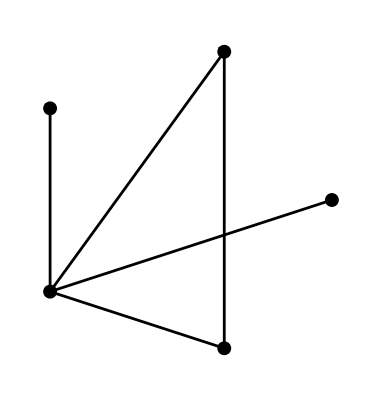

```mathematica
Ar={{3,2},{3,1},{3,4},{3,5} ,{1,4}};
G=FromUnorderedPairs[Ar];
ShowLabeledGraph[G]
```

Podem dibuixar el mateix graf sense les etiquetes dels vertexs fent

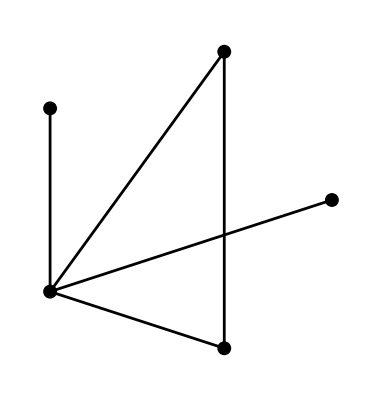

```mathematica
ShowGraph[G]
```

Donat un graf podem recuperar la llista d'arestes amb la instrucció Edges:

```mathematica
Edges[G]
```

{{2,3},{1,3},{3,4},{3,5},{1,4}}

Hi ha molts tipus de grafs importants que tenen nom propi, com per exemple els grafs complets K_n, els grafs cíclics C_n, els grafs estrella, els grafs roda, el graf buit d'ordre n, etc. Aquests grafs es poden generar amb Mathematica de la manera següent:

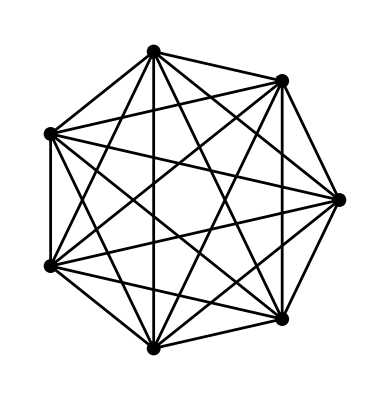

```mathematica
ShowLabeledGraph[CompleteGraph[7]]
```

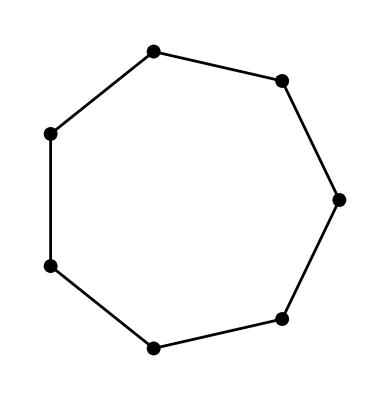

```mathematica
ShowLabeledGraph[Cycle[7]]
```

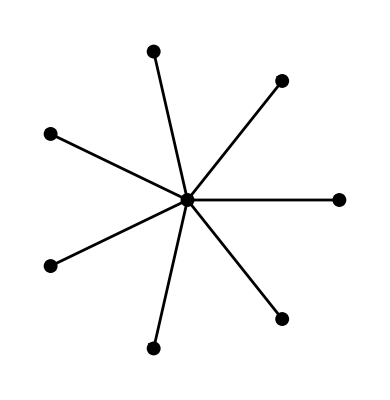

```mathematica
ShowLabeledGraph[Star[8]]
```

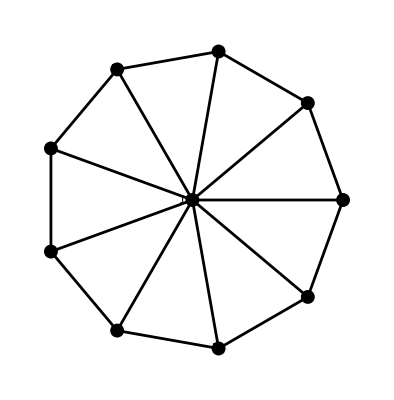

```mathematica
ShowLabeledGraph[Wheel[10]]
```

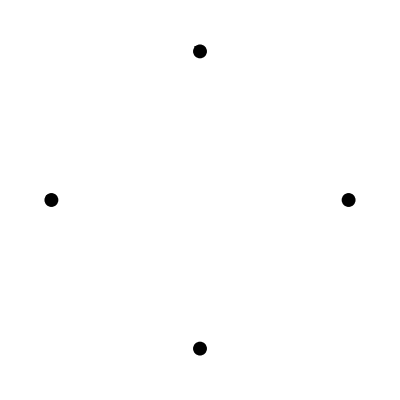

```mathematica
ShowLabeledGraph[EmptyGraph[4]]
```

#### Exercici 1

Dibuixeu i trobeu les llistes d'arestes del graf complet K_5, el graf cíclic C_6 i el graf roda de 7 vèrtexs.

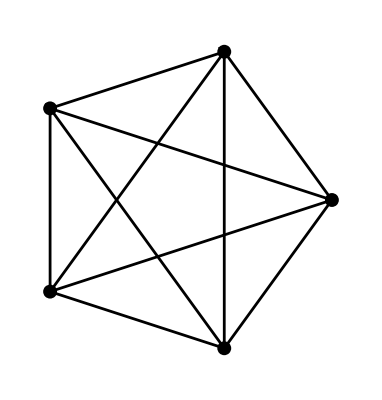

```mathematica
ShowLabeledGraph[CompleteGraph[5]]
```

```mathematica
Edges[CompleteGraph[5]]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

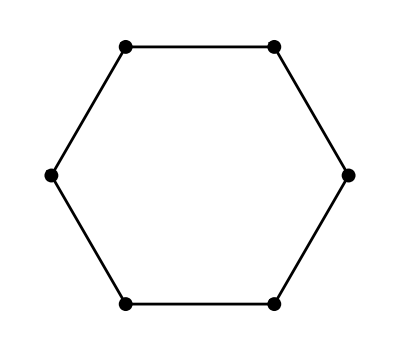

```mathematica
ShowLabeledGraph[Cycle[6]]
```

```mathematica
Edges[Cycle[6]]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{1,6}}

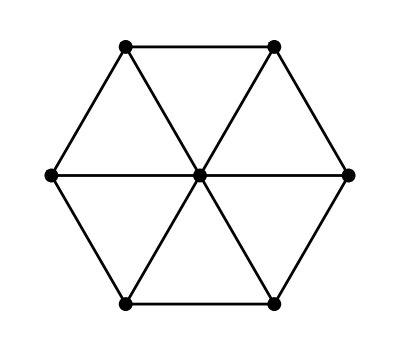

```mathematica
ShowLabeledGraph[Wheel[7]]
```

```mathematica
Edges[Wheel[7]]
```

{{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,2},{2,3},{3,4},{4,5},{5,6},{1,6}}

Isomorfismes de grafs

Definim un graf donant la seva llista d'arestes

```mathematica
G1=FromUnorderedPairs[{{1,2},{2,3},{1,3},{1,4},{1,5}}]
```

⁃Graph:<5,5,Undirected>⁃

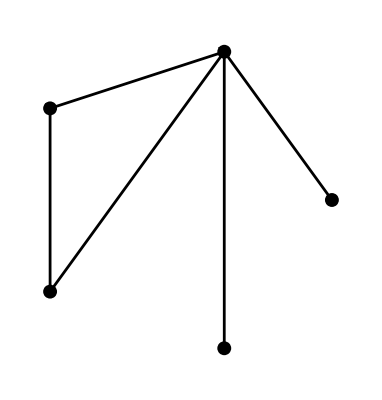

```mathematica
ShowLabeledGraph[G1]
```

Definim un altre graf a partir de la seva llista d'adjacències

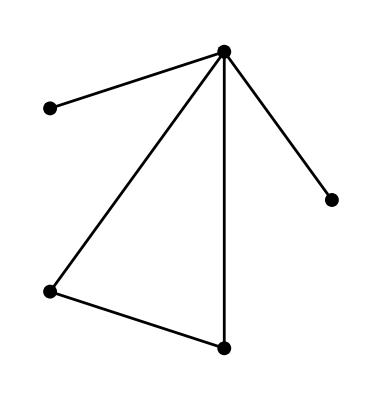

```mathematica
G2=FromUnorderedPairs[{{1,2},{1,5},{1,3},{3,4},{1,4}}];
ShowLabeledGraph[G2]
```

Observeu que els dibuixos són diferents, no obstant els grafs són isomorfs, tal i com ens diu la funció IsomorphicQ[,]:

```mathematica
IsomorphicQ[G1,G2]
```

True

Per trobar un isomorfisme podem fer servir la funció Isomorphism[,]:

```mathematica
?Isomorphism
Isomorphism[G1,G2]
```

Isomorphism[g,h] gives an isomorphism between graphs g and h if one exists. 
Isomorphism[g,h,All] gives all isomorphisms between graphs g and h. 
Isomorphism[g] gives the automorphism group of g.

{1,3,4,2,5}

#### Exercici 2

Considereu el graf següent.

Information::notfound: Symbol "FiniteGraph" not found.

⁃Graph:<12,8,Undirected>⁃

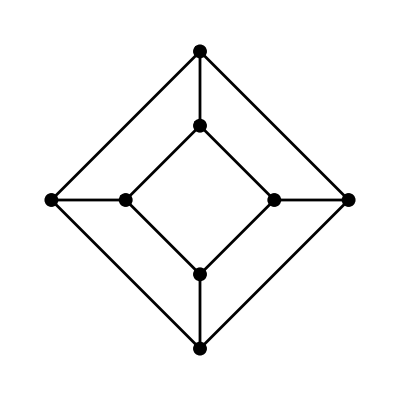

```mathematica
G3=FiniteGraphs[[3]]
ShowLabeledGraph[G3]
```

Definiu el graf G4 representat a sota i decidiu si és isomorf a G3.En cas que ho sigui, trobeu un isomorfisme.

```mathematica
L={{1,2},{1,4},{1,6},{2,3},{2,7},{3,4},{3,8},{4,9},{6,7},{6,9},{7,8},{8,9}};
```

```mathematica
G4=FromUnorderedPairs[L]
```

⁃Graph:<12,9,Undirected>⁃

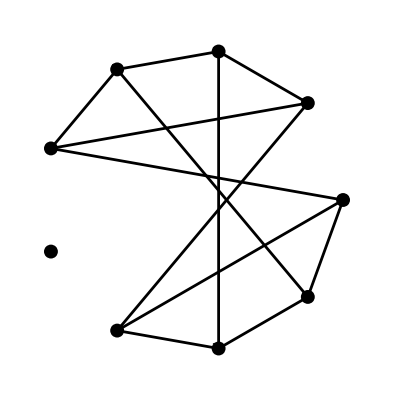

```mathematica
ShowLabeledGraph[G4]
```

```mathematica
Isomorphism[G3,G4]
```

{}

#### Exercici 3

Calculeu la llista d’excentricitats, centre, diàmetre i radi, d’alguns dels grafs següents.

```mathematica
L={{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}
G5=FromUnorderedPairs[L]
```

{{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}}

⁃Graph:<9,6,Undirected>⁃

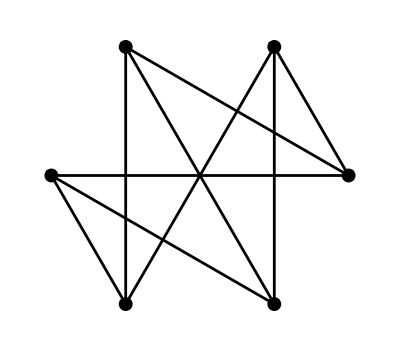

```mathematica
ShowLabeledGraph[G5]
```

```mathematica
Eccentricity[G5]
```

{2,2,2,2,2,2}

```mathematica
Diameter[G5]
```

2

```mathematica
Radius[G5]
```

2